Luke Wolcott
Math 125 Practice Notebook, for class tutorial

Every workbook is divided into cells, which you evaluate individually.  You can always change any cell input, but then you may need to reevaluate other cells as well.

Remember:
1. Use SHIFT-ENTER to evaluate a cell.
2. Delete a cell by clicking on its bracket on the far right and hitting DELETE.  You can also click and drag to select multiple cells, if you start to the far left.
3. Mathematica functions are capitalized, and use square brackets for input.  
4. Make sure to put spaces between variables like “a x + b”, or else it thinks the variable is named ax.
5. You don’t need to memorize many function names and syntax, just know how to look them up!
6. You can get function syntax by evaluating, e.g. “?Plot”.
7. Putting a semicolon after a line will “mute” the output.  This is a way of entering multiple lines at once.
8. The syntax for defining a function is, for example, “f[x_] := 3x^2”.
9. To “reset” a variable x, use Clear[x].

On your assignments:
0. Save often.
1. Use plain text cells to give your name and the assignment name at the top.
2. Don’t hesitate to make a mess at first.  But eventually delete any unnecessary cells.
3. Add plain text cells with explanation whenever necessary or helpful.  This blend of computed code and readable exposition is called “literate programming”.
4. Generally clean up your workbook, so it answers the questions clearly and succinctly.
5. When you submit your file, give it a filename with your last name, like “wolcott.nb” or “wolcott-1.nb”.

```mathematica
a=4
```

4

```mathematica
b=6
```

6

```mathematica
a+b
```

10

If I change the value stored in “a”, I need to reevaluate a+b.

One way to play around with Mathematica is to look at the options that Mathematica suggests you evaluate an input.  This is a fun way to learn new functions.

```mathematica
a^2 + b
```

22

```mathematica
Divisors[22]
```

{1,2,11,22}

```mathematica
Mean[{1,2,11,22}]
```

9

```mathematica
FactorInteger[22]
```

{{2,1},{11,1}}

Notice that all Mathematica function names are capitalized, and use square brackets [ ].
To enter text cells, click the + symbol at the top left of a new cell, and choose “Plain text”.

Suppose I want to do something, say plot a function, but don’t know the syntax or function name.  Some options:

1. Google “mathematica plot”.  Usually one of the first few search entries will be a page describing the function and how to use it.

2. Try to guess the function name by typing directly into Mathematica.  It will try to guess what function you want to use, and give you other functions with similar names.

3. If you have the function name -- Plot -- but not the syntax, you can ask Mathematica with “?Plot”.  This gives a quick summary of functionality and syntax.  By clicking on “>>” a help window will pop up, with simple examples.  These are super helpful and will usually tell you what you want to know.  

4. Find a similar example, copy and paste it, and tweak it to do what you want.

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

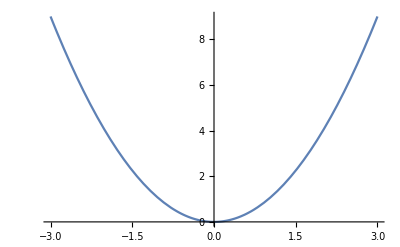

```mathematica
Plot[x^2, {x, -3, 3}]
```

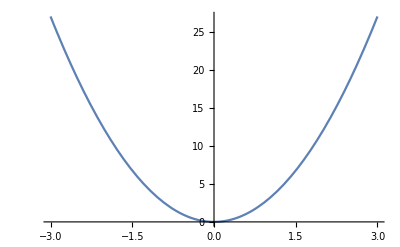

```mathematica
f[x_] := 3x^2;
Plot[f[x], {x, -3,3}]
```

Notice that I defined the function f, used a semicolon on the first line, and then plotted it in the second line.  This function definition syntax is a little odd.  Using a semicolon “mutes” the output.

Now suppose we want to calculate the derivative of f, but don’t know the function for that.  

What should we do?

Additional features to discuss:
1. Manipulate: for generating slider bars on plots. (sin x to demo; see below)
2. Wolfram|Alpha: using “==”, just for fun.

```mathematica
Manipulate[Plot[{Sin[x],a Sin[b x + c]+d}, {x,-2Pi,2Pi}, ImageSize->Full],{{a,1,"a = Amplitude"},-3,3},{{b,1,"b = Frequency"},0,4},{{c,0,"c = Horiz Shift"},-Pi,Pi}, {{d,0,"d = Vert Shift"},-2,2}]
```